## Funciones

```mathematica
(*Definición de la Matriz de rotación "Q" y el vector desplazamoiento "a"*)

Q[alpha_,theta_]:={{Cos[theta],-Sin[theta]*Cos[alpha],Sin[theta]*Sin[alpha]},{Sin[theta],Cos[theta]*Cos[alpha],-Cos[theta]*Sin[alpha]},{0,Sin[alpha],Cos[alpha]}};

c[theta_,a_,b_]:={a*Cos[theta],a*Sin[theta],b};

(***Transformación general*******************)
Aij[ai_,bi_,αi_,θi_]:={{Cos[θi],-Sin[θi]*Cos[αi],Sin[θi]*Sin[αi],ai*Cos[θi]},{Sin[θi],Cos[θi]*Cos[αi],-Cos[θi]*Sin[αi],ai*Sin[θi]},{0,Sin[αi],Cos[αi],bi},{0,0,0,1}};

(***Matriz de rotación*******************)
Rij[αi_,θi_]:={{Cos[θi],Sin[θi],0},{-Cos[αi]*Sin[θi],Cos[αi]*Cos[θi],Sin[αi]},{Sin[αi]*Sin[θi],-Sin[αi]*Cos[θi],Cos[αi]}};

Corrido
```

Corrido

## Ecuaciones

### Ecuaciones de posición

```mathematica
(*Transformación de {0} a {1}*)
Subscript[A, 0,1]=Aij[0,b1,Pi/2,θ1];MatrixForm[Subscript[A, 0,1]]
Subscript[p, 0,1]={Subscript[A, 0,1][[1,4]],Subscript[A, 0,1][[2,4]],Subscript[A, 0,1][[3,4]]};MatrixForm[Subscript[p, 0,1]]
```

(Cos[θ1] | 0 | Sin[θ1] | 0
Sin[θ1] | 0 | -Cos[θ1] | 0
0 | 1 | 0 | b1
0 | 0 | 0 | 1)

(0
0
b1)

```mathematica
(*Transformación de {1} a {2}*)

Subscript[A, 1,2]=Aij[a2,0,0,θ2+Pi/2];MatrixForm[Subscript[A, 1,2]]
Subscript[p, 1,2]={Subscript[A, 1,2][[1,4]],Subscript[A, 1,2][[2,4]],Subscript[A, 1,2][[3,4]]};MatrixForm[Subscript[p, 1,2]]
```

(-Sin[θ2] | -Cos[θ2] | 0 | -a2 Sin[θ2]
Cos[θ2] | -Sin[θ2] | 0 | a2 Cos[θ2]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(-a2 Sin[θ2]
a2 Cos[θ2]
0)

```mathematica
(*Transformación de {1} a {2}*)

Subscript[A, 2,3]=Aij[a3,0,0,θ3-Pi/2];MatrixForm[Subscript[A, 2,3]]
Subscript[p, 2,3]={Subscript[A, 2,3][[1,4]],Subscript[A, 2,3][[2,4]],Subscript[A, 2,3][[3,4]]};MatrixForm[Subscript[p, 2,3]]
```

(Sin[θ3] | Cos[θ3] | 0 | a3 Sin[θ3]
-Cos[θ3] | Sin[θ3] | 0 | -a3 Cos[θ3]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(a3 Sin[θ3]
-a3 Cos[θ3]
0)

```mathematica
Subscript[A, 0,3]=Simplify[Subscript[A, 0,1].Subscript[A, 1,2].Subscript[A, 2,3]];MatrixForm[Subscript[A, 0,3]]
Subscript[p, 0,3]={Subscript[A, 0,3][[1,4]],Subscript[A, 0,3][[2,4]],Subscript[A, 0,3][[3,4]]};MatrixForm[Subscript[p, 0,3]]
```

(Cos[θ1] Cos[θ2+θ3] | -Cos[θ1] Sin[θ2+θ3] | Sin[θ1] | Cos[θ1] (a3 Cos[θ2+θ3]-a2 Sin[θ2])
Cos[θ2+θ3] Sin[θ1] | -Sin[θ1] Sin[θ2+θ3] | -Cos[θ1] | Sin[θ1] (a3 Cos[θ2+θ3]-a2 Sin[θ2])
Sin[θ2+θ3] | Cos[θ2+θ3] | 0 | b1+a2 Cos[θ2]+a3 Sin[θ2+θ3]
0 | 0 | 0 | 1)

(Cos[θ1] (a3 Cos[θ2+θ3]-a2 Sin[θ2])
Sin[θ1] (a3 Cos[θ2+θ3]-a2 Sin[θ2])
b1+a2 Cos[θ2]+a3 Sin[θ2+θ3])

```mathematica
Subscript[A, 0,2]=Simplify[Subscript[A, 0,1].Subscript[A, 1,2]];MatrixForm[Subscript[A, 0,2]]
Subscript[p, 0,2]={Subscript[A, 0,2][[1,4]],Subscript[A, 0,2][[2,4]],Subscript[A, 0,2][[3,4]]};MatrixForm[Subscript[p, 0,2]]
```

(-Cos[θ1] Sin[θ2] | -Cos[θ1] Cos[θ2] | Sin[θ1] | -a2 Cos[θ1] Sin[θ2]
-Sin[θ1] Sin[θ2] | -Cos[θ2] Sin[θ1] | -Cos[θ1] | -a2 Sin[θ1] Sin[θ2]
Cos[θ2] | -Sin[θ2] | 0 | b1+a2 Cos[θ2]
0 | 0 | 0 | 1)

(-a2 Cos[θ1] Sin[θ2]
-a2 Sin[θ1] Sin[θ2]
b1+a2 Cos[θ2])

### Matrices de la cinemática

```mathematica
(*Matriz Jacobiana*)
J={{D[Subscript[x, p][[1]], θ1],D[Subscript[x, p][[1]], θ2],D[Subscript[x, p][[1]], θ3]},{D[Subscript[x, p][[2]], θ1],D[Subscript[x, p][[2]], θ2],D[Subscript[x, p][[2]], θ3]},{D[Subscript[x, p][[3]], θ1],D[Subscript[x, p][[3]], θ2],D[Subscript[x, p][[3]], θ3]}};
MatrixForm[J]

(*Matriz Hessiana*)
H={{D[Subscript[x, p][[1]], θ1,θ1],D[Subscript[x, p][[1]], θ2,θ1],D[Subscript[x, p][[1]], θ3,θ1]},{D[Subscript[x, p][[2]], θ1,θ2],D[Subscript[x, p][[2]], θ2,θ2],D[Subscript[x, p][[2]], θ3,θ2]},{D[Subscript[x, p][[3]], θ1,θ3],D[Subscript[x, p][[3]], θ2,θ3],D[Subscript[x, p][[3]], θ3,θ3]}};
MatrixForm[H]
```

Part::partw: Part 3 of x_p does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

Part::partw: Part 3 of x_p does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

## Puntos a interpolar

```mathematica
Subscript[x, 0]=0.9;Subscript[f, 0]=1.3; 
Subscript[x, 1]=1.3;Subscript[f, 1]=1.5;
Subscript[x, 2]=1.9;Subscript[f, 2]=1.85;
Subscript[x, 3]=2.1;Subscript[f, 3]=2.1;
Subscript[x, 4]=2.6;Subscript[f, 4]=2.6;
Subscript[x, 5]=3;Subscript[f, 5]=2.7;
Subscript[x, 6]=3.9;Subscript[f, 6]=2.4;
Subscript[x, 7]=4.4;Subscript[f, 7]=2.15;
Subscript[x, 8]=4.7;Subscript[f, 8]=2.05;
Subscript[x, 9]=5.0;Subscript[f, 9]=2.1;
Subscript[x, 10]=6.0;Subscript[f, 10]=2.25;
Subscript[x, 11]=7.0;Subscript[f, 11]=2.3;
Subscript[x, 12]=8;Subscript[f, 12]=2.25;
Subscript[x, 13]=9.2;Subscript[f, 13]=1.95;
Subscript[x, 14]=10.5;Subscript[f, 14]=1.4;
Subscript[x, 15]=11.3;Subscript[f, 15]=0.9;
Subscript[x, 16]=11.6;Subscript[f, 16]=0.7;
Subscript[x, 17]=12;Subscript[f, 17]=0.6;
Subscript[x, 18]=12.6;Subscript[f, 18]=0.5;
Subscript[x, 19]=13;Subscript[f, 19]=0.4;
Subscript[x, 20]=13.3;Subscript[f, 20]=0.25;
Corrido
```

Corrido

### Acondicionamiento de datos

```mathematica
n=20;
 
(*numero de puntos*)

For[t=0,t≤n,t++, Subscript[a, t]=Subscript[f, t];];
Corrido
Subscript[a, 0]
Subscript[a, 20]
```

Corrido

1.3

0.25

### Paso 1

```mathematica
(*Obtención del valor de los intervalos h*)
For[t=0,t≤n-1,t++,

Subscript[h, t]=Subscript[x, t+1]-Subscript[x, t];
];
Subscript[h, 0]
Subscript[h, 19]
```

0.4

0.3

### Paso 2

```mathematica
(*Que forman el vector b*)

For[i=1,i≤n-1,i++,

Subscript[α, i]=(3*(Subscript[a, i+1]-Subscript[a, i]))/Subscript[h, i]-(3*(Subscript[a, i]-Subscript[a, i-1]))/Subscript[h, i-1];
];

Subscript[α, 1]
Subscript[α, 19]
```

0.25

-0.75

### Paso 3

```mathematica
(*Valores de terminados para el método de invertir la matriz, condiciones iniciales*)

Subscript[l, 0]=1;
Subscript[μ, 0]=0;
Subscript[z, 0]=0;
CORRIDO
```

CORRIDO

### Paso 4

```mathematica
For[i=1,i≤n-1,i++,

Subscript[l, i]=2*(Subscript[x, i+1]-Subscript[x, i-1])-Subscript[h, i-1]*Subscript[μ, i-1];
Subscript[μ, i]=Subscript[h, i]/Subscript[l, i];
Subscript[z, i]=(Subscript[α, i]-Subscript[h, i-1]*Subscript[z, i-1])/Subscript[l, i];
];
CORRIDO
```

CORRIDO

### Paso 5

```mathematica
(*Condiciones finales*)

Subscript[l, n]=1;
Subscript[c, n]=0;
Subscript[z, n]=0;
CORRIDO
```

CORRIDO

### Paso 6

```mathematica
i=n-1;
For[t=0,t≤n-1,t++,

Subscript[c, i]=Subscript[z, i]-Subscript[μ, i]*Subscript[c, i+1];
Subscript[b, i]=(Subscript[a, i+1]-Subscript[a, i])/Subscript[h, i]-(Subscript[h, i]*(Subscript[c, i+1]+2*Subscript[c, i]))/3;
Subscript[d, i]=(Subscript[c, i+1]-Subscript[c, i])/(3*Subscript[h, i]);
i=i-1;

];
CORRIDO
```

CORRIDO

```mathematica
Subscript[a, 0]
Subscript[b, 0]
Subscript[c, 0]
Subscript[d, 0]
```

1.3

0.539624

0.

-0.247649

### Arreglo de los segementos

```mathematica
tf=0.5;
For[i=0,i≤n-1,i++,
PN[i]=Table[{Subscript[x, i]+(10/tf^3*t^3-15/tf^4*t^4+6/tf^5*t^5)*(Subscript[x, i+1]-Subscript[x, i]),Subscript[a, i]+Subscript[b, i]*((Subscript[x, i]+(10/tf^3*t^3-15/tf^4*t^4+6/tf^5*t^5)*(Subscript[x, i+1]-Subscript[x, i]))-Subscript[x, i])+Subscript[c, i]*((Subscript[x, i]+(10/tf^3*t^3-15/tf^4*t^4+6/tf^5*t^5)*(Subscript[x, i+1]-Subscript[x, i]))-Subscript[x, i])^2+Subscript[d, i]((Subscript[x, i]+(10/tf^3*t^3-15/tf^4*t^4+6/tf^5*t^5)*(Subscript[x, i+1]-Subscript[x, i]))-Subscript[x, i])^3 },{t,0,tf,0.1}];
];
```

### Pegando los arreglos

```mathematica
PoT=Join[PN[0],PN[1],PN[2],PN[3],PN[4],PN[5],PN[6],PN[7],PN[8],PN[9],PN[10],PN[11],PN[12],PN[13],PN[14],PN[15],PN[16],PN[17],PN[18],PN[19]];
```

### Graficaciones

```mathematica
(*Ima=Grafica[PoT,"x","f(x)",0,0.5,1];
Show[Ima]*)

PoT3D=Table[Flatten[{PoT[[i]],2.5}],{i,Length[PoT]}];
tray=Graphics3D[Line[PoT3D]]
```

-Graphics3D-

## Solución de la trayectoria

### Solución inicial

```mathematica
xe=0;
ye=0;
ze=0;

b1=0.085;
a2=0.25;
a3=0.2875;
Solin=FindRoot[{Cos[θ1]*(a3*Cos[θ2+θ3]-a2*Sin[θ2])==0.1,
Sin[θ1]*(a3*Cos[θ2+θ3]-a2*Sin[θ2])==0.2,
b1+a2 Cos[θ2]+a3 Sin[θ2+θ3]==0.0
},
{θ1,40*Degree},
{θ2,100*Degree},
{θ3,-60*Degree}
]

{θ1/.Solin,θ2/.Solin,θ3/.Solin}/Degree
```

{θ1→-1.24905,θ2→0.684059,θ3→-2.09668}

{-71.5651,39.1937,-120.131}

### Solución general

```mathematica
θ1a=θ1/.Solin;
θ2a=θ2/.Solin;
θ3a=θ3/.Solin;

For[i=1,i≤Length[PoT],i++,
Solgen[i]=FindRoot[{Subscript[p, 0,3][[1]]+xe==PoT3D[[i,1]],
Subscript[p, 0,3][[2]]+ye==PoT3D[[i,2]],
Subscript[p, 0,3][[3]]+ze==PoT3D[[i,3]]
},
{θ1,θ1a},
{θ2,θ2a},
{θ3,θ3a}
];

θ1a=θ1/.Solgen[i];
θ2a=θ2/.Solgen[i];
θ3a=θ3/.Solgen[i];

];
```

## Cinemática inversa (posición)

```mathematica
c0={xe,ye,ze}

Manipulate[

linea1=Line[{{0,0,0}+c0,c0+Subscript[p, 0,1]}];
linea2=Line[{c0+Subscript[p, 0,1],c0+Subscript[p, 0,2]}];
linea3=Line[{c0+Subscript[p, 0,2],c0+Subscript[p, 0,3]}];

barra1=Graphics3D[{AbsoluteThickness[4],RGBColor[1,0,0],linea1}]/.Solgen[i];
barra2=Graphics3D[{AbsoluteThickness[4],RGBColor[0,1,0],linea2}]/.Solgen[i];
barra3=Graphics3D[{AbsoluteThickness[4],RGBColor[0,0,1],linea3}]/.Solgen[i];

Show[barra1,barra2,barra3,tray,Axes->True,AxesLabel->{"x","y","z"},ImageSize->300,BaseStyle->{24,FontFamily->"Arial"},PlotRange->{{-1,15},{-4,9},{-5,9}}],{i,1,Length[PoT3D],1}]
```

{2,-2,0}

## Cálculo de las velocidades

### Arreglo de los segementos velocidad

```mathematica
tf=0.5;
For[i=0,i≤n-1,i++,

tc[i]=tf*i;
VPN[i]=Table[{(3 10/tf^3*t^2-4 15/tf^4*t^3+5 6/tf^5*t^4)*(Subscript[x, i+1]-Subscript[x, i]),((30 t^4)/tf^5-(60 t^3)/tf^4+(30 t^2)/tf^3) Subscript[b, i] (-Subscript[x, i]+Subscript[x, 1+i])+2 ((30 t^4)/tf^5-(60 t^3)/tf^4+(30 t^2)/tf^3) ((6 t^5)/tf^5-(15 t^4)/tf^4+(10 t^3)/tf^3) Subscript[c, i] (-Subscript[x, i]+Subscript[x, 1+i])^2+3 ((30 t^4)/tf^5-(60 t^3)/tf^4+(30 t^2)/tf^3) ((6 t^5)/tf^5-(15 t^4)/tf^4+(10 t^3)/tf^3)^2 Subscript[d, i] (-Subscript[x, i]+Subscript[x, 1+i])^3,tc[i]+t},{t,0,tf,0.1}];
];
```

### Pegando los arreglos velocidad

```mathematica
VPoT=Join[VPN[0],VPN[1],VPN[2],VPN[3],VPN[4],VPN[5],VPN[6],VPN[7],VPN[8],VPN[9],VPN[10],VPN[11],VPN[12],VPN[13],VPN[14],VPN[15],VPN[16],VPN[17],VPN[18],VPN[19]];
```

### Arreglo de los segementos Aceleración

```mathematica
tf=0.5;
For[i=0,i≤n-1,i++,
tc[i]=tf*i;

APN[i]=Table[{(6 10/tf^3*t-12 15/tf^4*t^2+20 6/tf^5*t^3)*(Subscript[x, i+1]-Subscript[x, i]),((120 t^3)/tf^5-(180 t^2)/tf^4+(60 t)/tf^3) Subscript[b, i] (-Subscript[x, i]+Subscript[x, 1+i])+2 ((30 t^4)/tf^5-(60 t^3)/tf^4+(30 t^2)/tf^3)^2 Subscript[c, i] (-Subscript[x, i]+Subscript[x, 1+i])^2+2 ((120 t^3)/tf^5-(180 t^2)/tf^4+(60 t)/tf^3) ((6 t^5)/tf^5-(15 t^4)/tf^4+(10 t^3)/tf^3) Subscript[c, i] (-Subscript[x, i]+Subscript[x, 1+i])^2+6 ((30 t^4)/tf^5-(60 t^3)/tf^4+(30 t^2)/tf^3)^2 ((6 t^5)/tf^5-(15 t^4)/tf^4+(10 t^3)/tf^3) Subscript[d, i] (-Subscript[x, i]+Subscript[x, 1+i])^3+3 ((120 t^3)/tf^5-(180 t^2)/tf^4+(60 t)/tf^3) ((6 t^5)/tf^5-(15 t^4)/tf^4+(10 t^3)/tf^3)^2 Subscript[d, i] (-Subscript[x, i]+Subscript[x, 1+i])^3,tc[i]+t},{t,0,tf,0.1}];
];
```

### Pegando los arreglos Aceleración

```mathematica
APoT=Join[APN[0],APN[1],APN[2],APN[3],APN[4],APN[5],APN[6],APN[7],APN[8],APN[9],APN[10],APN[11],APN[12],APN[13],APN[14],APN[15],APN[16],APN[17],APN[18],APN[19]];
```

## Velocidad y aceleración en el espacio del robot

### Velocidad

```mathematica
For[i=1,i≤Length[VPoT],i++,

Ja[i]=J/.Solgen[i];
qp[i]=Inverse[Ja[i]].{VPoT[[i,1]],VPoT[[i,2]],0};

];
```

### Graficas de la velocidad

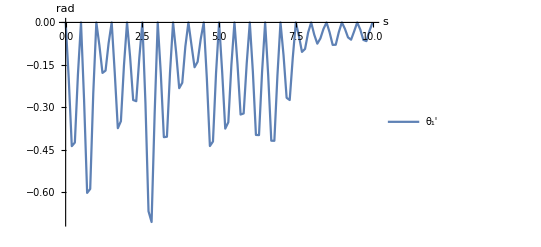

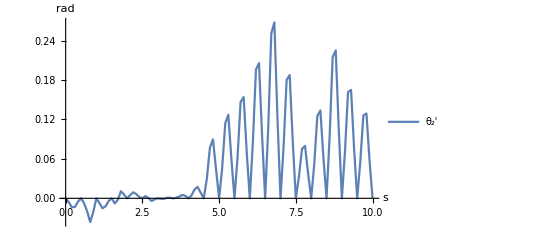

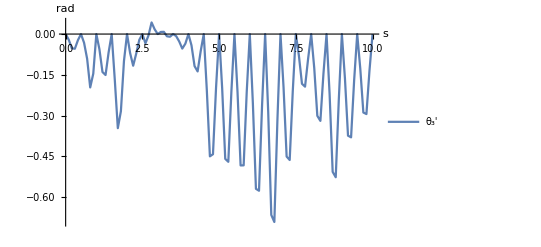

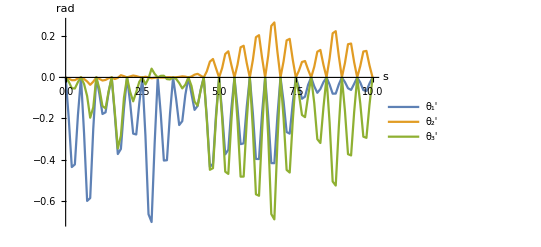

```mathematica
Velocidadθ1=ListPlot[Table[{VPoT[[i,3]],qp[i][[1]]},{i,1,Length[VPoT],1}],Joined->True,PlotLegends->{Subscript[θ, 1]'},AxesLabel->{"s","rad"}]
Velocidadθ2=ListPlot[Table[{VPoT[[i,3]],qp[i][[2]]},{i,1,Length[VPoT],1}],Joined->True,PlotLegends->{Subscript[θ, 2]'},AxesLabel->{"s","rad"}]
Velocidadθ3=ListPlot[Table[{VPoT[[i,3]],qp[i][[3]]},{i,1,Length[VPoT],1}],Joined->True,PlotLegends->{Subscript[θ, 3]'},AxesLabel->{"s","rad"}]

Velocidadesang=ListPlot[{Table[{VPoT[[i,3]],qp[i][[1]]},{i,1,Length[VPoT],1}],Table[{VPoT[[i,3]],qp[i][[2]]},{i,1,Length[VPoT],1}],Table[{VPoT[[i,3]],qp[i][[3]]},{i,1,Length[VPoT],1}]},Joined->True,PlotLegends->{Subscript[θ, 1]',Subscript[θ, 2]',Subscript[θ, 3]'},AxesLabel->{"s","rad"}]
```

### Aceleración

```mathematica
For[i=1,i≤Length[VPoT],i++,

Ja[i]=J/.Solgen[i];
Ha[i]=H/.Solgen[i];

qpp[i]=Inverse[Ja[i]].({APoT[[i,1]],APoT[[i,2]],0}-Ha[i].qp[i]);

];
```

### Graficas de la velocidad

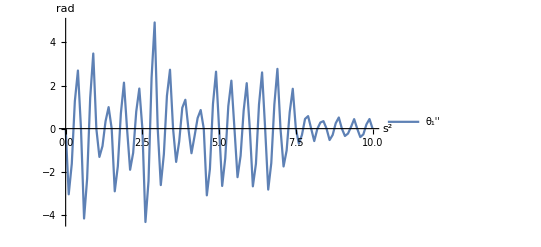

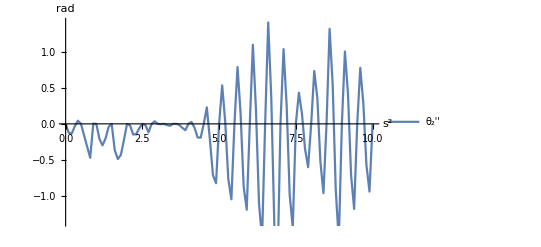

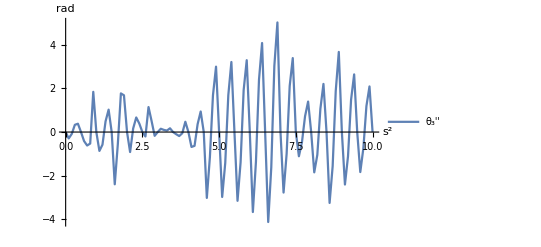

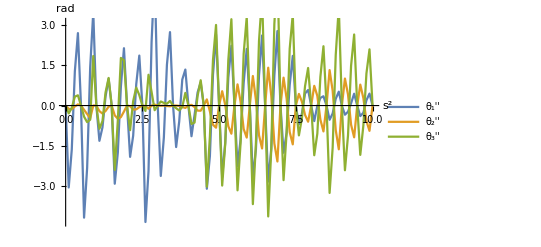

```mathematica
Acelθ1=ListPlot[Table[{APoT[[i,3]],qpp[i][[1]]},{i,1,Length[APoT],1}],Joined->True,PlotLegends->{Subscript[θ, 1]''},AxesLabel->{"s^2","rad"}]
Acelθ2=ListPlot[Table[{APoT[[i,3]],qpp[i][[2]]},{i,1,Length[APoT],1}],Joined->True,PlotLegends->{Subscript[θ, 2]''},AxesLabel->{"s^2","rad"}]
Acelθ3=ListPlot[Table[{APoT[[i,3]],qpp[i][[3]]},{i,1,Length[APoT],1}],Joined->True,PlotLegends->{Subscript[θ, 3]''},AxesLabel->{"s^2","rad"}]

Acelang=ListPlot[{Table[{APoT[[i,3]],qpp[i][[1]]},{i,1,Length[APoT],1}],Table[{APoT[[i,3]],qpp[i][[2]]},{i,1,Length[APoT],1}],Table[{APoT[[i,3]],qpp[i][[3]]},{i,1,Length[APoT],1}]},Joined->True,PlotLegends->{Subscript[θ, 1]'',Subscript[θ, 2]'',Subscript[θ, 3]''},AxesLabel->{"s^2","rad"}]
```